```mathematica
$Assumptions={k>0,κ>0,a>0,κ<1};
Integrate[(a^2 √((k^2-2κ)^2-4))/(√(1+a^4-2κ a^2)(a^4+(k^2-2κ)a^2+1)),a]
%/.{a->0}
ans = %%//FullSimplify
```

(ⅈ √((-4+(k^2-2 κ)^2)/(1+a^4-2 a^2 κ)) √(1+a^2/(-κ+√(-1+κ^2))) √(1-a^2/(κ+√(-1+κ^2))) (EllipticPi[(2 (κ-√(-1+κ^2)))/(-k^2+√(-4+(k^2-2 κ)^2)+2 κ),ⅈ ArcSinh[a √(1/(-κ+√(-1+κ^2)))],(κ-√(-1+κ^2))/(κ+√(-1+κ^2))]-EllipticPi[(2 (-κ+√(-1+κ^2)))/(k^2+√(-4+(k^2-2 κ)^2)-2 κ),ⅈ ArcSinh[a √(1/(-κ+√(-1+κ^2)))],(κ-√(-1+κ^2))/(κ+√(-1+κ^2))]))/(√(-4+(k^2-2 κ)^2) √(1/(-κ+√(-1+κ^2))))

0

1/(√(1/(-κ+√(-1+κ^2))))ⅈ √(1/(1+a^2 (-κ+√(-1+κ^2)))) √(1-a^2/(κ+√(-1+κ^2))) (EllipticPi[(2 (κ-√(-1+κ^2)))/(-k^2+√(-4+(k^2-2 κ)^2)+2 κ),ⅈ ArcSinh[a √(1/(-κ+√(-1+κ^2)))],-1+2 κ (κ-√(-1+κ^2))]-EllipticPi[(2 (-κ+√(-1+κ^2)))/(k^2+√(-4+(k^2-2 κ)^2)-2 κ),ⅈ ArcSinh[a √(1/(-κ+√(-1+κ^2)))],-1+2 κ (κ-√(-1+κ^2))])

```mathematica
(* https://mathematica.stackexchange.com/a/51060 *)
PowerContract[expr_]:=expr//.{m_^q_ n_^q_:>(m n)^q/;!IntegerQ[m]&&!IntegerQ[n],m_^q_ n_^p_:>(m/n)^q/;q>=0&&p==-q&&!IntegerQ[m]&&!IntegerQ[n]}
```

```mathematica
ans//PowerContract//FullSimplify
```

ⅈ √(-κ+√(-1+κ^2)) (EllipticPi[(2 (κ-√(-1+κ^2)))/(-k^2+√(-4+(k^2-2 κ)^2)+2 κ),ⅈ ArcSinh[a √(1/(-κ+√(-1+κ^2)))],-1+2 κ (κ-√(-1+κ^2))]-EllipticPi[(2 (-κ+√(-1+κ^2)))/(k^2+√(-4+(k^2-2 κ)^2)-2 κ),ⅈ ArcSinh[a √(1/(-κ+√(-1+κ^2)))],-1+2 κ (κ-√(-1+κ^2))])

$Aborted

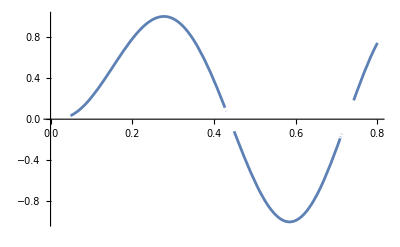

```mathematica
Plot[ Sin[k ⅈ √(-κ+√(-1+κ^2)) (EllipticPi[(2 (κ-√(-1+κ^2)))/(-k^2+√(-4+(k^2-2 κ)^2)+2 κ),ⅈ ArcSinh[a √(1/(-κ+√(-1+κ^2)))],-1+2 κ (κ-√(-1+κ^2))]-EllipticPi[(2 (-κ+√(-1+κ^2)))/(k^2+√(-4+(k^2-2 κ)^2)-2 κ),ⅈ ArcSinh[a √(1/(-κ+√(-1+κ^2)))],-1+2 κ (κ-√(-1+κ^2))])]/.k->10/.κ->0.5,{a,0,0.8}]
```